## Gradient Method for quadratic function

The following gmQuadratic is based on from https://mathematica.stackexchange.com/questions/208474/implement-gradient-method-in-functional-programming-style;

### Gradient Method with exact line search

```mathematica
gmQuadratic[A_,b_,x0_,eps_,iter_]:=
Module[{x,g,α,NormG,f,v,path},x=x0;
g=A.x+b;
v=1/2 x0.A.x0+b.x0;
α=N[(Norm[g]^2)/g.A.g];
NormG=Norm[g];
f[step_,α_,x_,g_,sqaureNormG_,v_]:={
step+1,(*update Iteration counts*)
N[Norm[g]^2/g.A.g],(*α step size*)
x-N[Norm[g]^2/g.A.g]*g,(*update x*)A.(x-N[Norm[g]^2/g.A.g]*g)+b,(*update gradient*)
Norm[A.(x-N[Norm[g]^2/g.A.g]*g)+b],(*update gradient norm*)
1/2 (x-N[Norm[g]^2/g.A.g]*g).A.(x-N[Norm[g]^2/g.A.g]*g)+b.(x-N[Norm[g]^2/g.A.g]*g)(*object function value*)};
path=NestWhileList[f[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]]&,{0,α,x,g,NormG,v},#[[1]]≤iter&&#[[5]]≥eps&];
gmQuadratic[TableHeadings]={"Iteration","Step Size","X","Gradient","Gradient Norm","Object Value"};
TableForm[path, TableHeadings->{None, gmQuadratic[TableHeadings]}]
]
```

### Demo

```mathematica
A={{2,0},{0,4}};
b={0,0};
x0={2,1};
```

```mathematica
gmQuadratic[A,b,x0,10^-6,100]
```

Iteration | Step Size | X | Gradient | Gradient Norm | Object Value
0 | 0.333333 | 2
1 | 4
4 | 4 √2 | 6
1 | 0.333333 | 0.666667
-0.333333 | 1.33333
-1.33333 | 1.88562 | 0.666667
2 | 0.333333 | 0.222222
0.111111 | 0.444444
0.444444 | 0.628539 | 0.0740741
3 | 0.333333 | 0.0740741
-0.037037 | 0.148148
-0.148148 | 0.209513 | 0.00823045
4 | 0.333333 | 0.0246914
0.0123457 | 0.0493827
0.0493827 | 0.0698377 | 0.000914495
5 | 0.333333 | 0.00823045
-0.00411523 | 0.0164609
-0.0164609 | 0.0232792 | 0.000101611
6 | 0.333333 | 0.00274348
0.00137174 | 0.00548697
0.00548697 | 0.00775975 | 0.0000112901
7 | 0.333333 | 0.000914495
-0.000457247 | 0.00182899
-0.00182899 | 0.00258658 | 1.25445×10^-6
8 | 0.333333 | 0.000304832
0.000152416 | 0.000609663
0.000609663 | 0.000862194 | 1.39383×10^-7
9 | 0.333333 | 0.000101611
-0.0000508053 | 0.000203221
-0.000203221 | 0.000287398 | 1.5487×10^-8
10 | 0.333333 | 0.0000338702
0.0000169351 | 0.0000677404
0.0000677404 | 0.0000957993 | 1.72078×10^-9
11 | 0.333333 | 0.0000112901
-5.64503×10^-6 | 0.0000225801
-0.0000225801 | 0.0000319331 | 1.91198×10^-10
12 | 0.333333 | 3.76335×10^-6
1.88168×10^-6 | 7.52671×10^-6
7.52671×10^-6 | 0.0000106444 | 2.12442×10^-11
13 | 0.333333 | 1.25445×10^-6
-6.27225×10^-7 | 2.5089×10^-6
-2.5089×10^-6 | 3.54812×10^-6 | 2.36047×10^-12
14 | 0.333333 | 4.1815×10^-7
2.09075×10^-7 | 8.36301×10^-7
8.36301×10^-7 | 1.18271×10^-6 | 2.62275×10^-13
15 | 0.333333 | 1.39383×10^-7
-6.96917×10^-8 | 2.78767×10^-7
-2.78767×10^-7 | 3.94236×10^-7 | 2.91416×10^-14

### Conjugate gradient method

```mathematica
cgMethod[A_,b_,x0_, tol_]:=
Module[
{r,r0,p0,α0, cg,x,xList},
r0=A.x0-b;
p0=-r0;
x[rOld_,xOld_,pOld_]:=xOld+Norm[rOld]^2/(pOld.A.pOld)*pOld;
r[rOld_,xOld_,pOld_]:=rOld+Norm[rOld]^2/(pOld.A.pOld)*A.pOld;

cg[{rOld_,xOld_,pOld_}]:={r[rOld,xOld,pOld],x[rOld,xOld,pOld],-r[rOld,xOld,pOld]+Norm[r[rOld,xOld,pOld]]^2/Norm[rOld]^2*pOld};
xList=NestWhileList[cg,{r0,x0,p0},Norm[#[[1]]]≥ tol&];
xList[[-1]]
];
```

```mathematica
A=With[{n=10},DiagonalMatrix[Range[1,n]]+ConstantArray[1,{n,n}]-IdentityMatrix[n]];
b=ConstantArray[1,10];
```

```mathematica
cgMethod[A,b, ConstantArray[0,10],10^-5][[2]]
```

{1,0,0,0,0,0,0,0,0,0}

## Gradient Method with backtracking

```mathematica
gmBackTracking[f_,g_,x0_,α0_,tol_]:=
Module[{x,gm,BackTracking,path,iter,stepCount,cluster,Δ},
x=x0;
BackTracking[x_]:=Module[
{ϕ0,ϕ1,x1,α,d,αcount,γ,σ},
α=α0;
ϕ0=f[x[[1]],x[[2]]];
d=-g[x[[1]],x[[2]]];
αcount=1;
x1=x+α*d;
ϕ1=f[x1[[1]],x1[[2]]];
γ= 0.1;σ= 0.5;
While[ϕ1>ϕ0-α *0.1* Norm[d]^2&& αcount≤100,α=0.5 α;αcount+=1;x1=x+α*d;ϕ1=f[x1[[1]],x1[[2]]]];
α
];
stepCount=0;
gm[{iter_,x_,ng_}]:={iter+1,x-BackTracking[x]*g[x[[1]],x[[2]]],N[Norm[g[x[[1]],x[[2]]]]]};
path=NestWhileList[gm,{stepCount,x,N[Norm[g[x[[1]],x[[2]]]]]},Norm[g[#[[2]][[1]],#[[2]][[2]]]]>tol&&#[[1]]≤10000&];
cluster[path_]:=path[[-1]][[2]];
Δ=Map[N[Norm[#]]&,Map[#[[2]]-cluster[path]&,path]];
gmBackTracking[TableHeadings]={"ITER","X_k","G.NORM"};
{TableForm[Take[path,-10],TableHeadings->{None, gmBackTracking[TableHeadings]}],TableForm[Take[Δ,-10]],
ListLogPlot[Transpose[path][[3]],Joined->True,PlotStyle->Red,ImageSize->Medium,AxesLabel->{"Iter","G.NORM"},PlotLabel->Row[{"Norm of gradient"}]],
ListLogPlot[Δ,Joined->True,PlotRange->All,ImageSize->Medium,AxesLabel->{"Iter","Δ"},PlotLabel->Row[{"Norm of x_k-x^*"}]]}
];
```

```mathematica
f1[x_,y_]:=x+((5-y) y-2) y-13
f2[x_,y_]:=x+((y+1) y-14) y-29
f[x_,y_]:=f1[x,y]^2+f2[x,y]^2
g[x_?NumberQ,y_?NumberQ]=Map[D[f[x,y],#]&,{x,y}]
```

{2 (-13+x+y (-2+(5-y) y))+2 (-29+x+y (-14+y (1+y))),2 (-2+(5-2 y) y+(5-y) y) (-13+x+y (-2+(5-y) y))+2 (-14+y (1+y)+y (1+2 y)) (-29+x+y (-14+y (1+y)))}

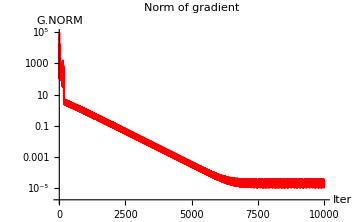
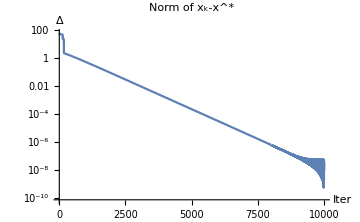
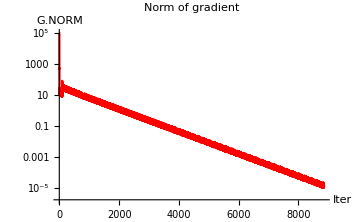
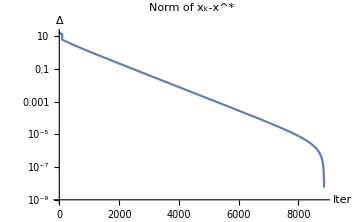
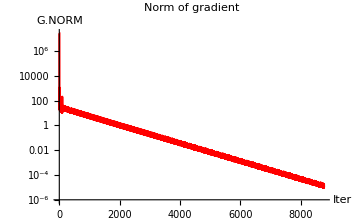
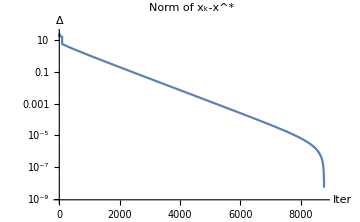
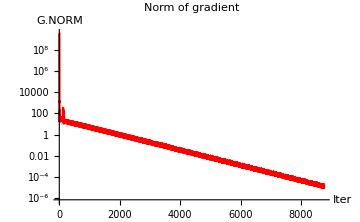
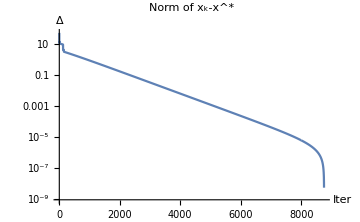
{{ITER | X_k | G.NORM
9992 | 11.4128
-0.896805 | 0.0000159671
9993 | 11.4128
-0.896805 | 0.0000122581
9994 | 11.4128
-0.896805 | 0.0000310793
9995 | 11.4128
-0.896805 | 0.0000238599
9996 | 11.4128
-0.896805 | 0.0000183174
9997 | 11.4128
-0.896805 | 0.0000140625
9998 | 11.4128
-0.896805 | 0.0000107959
9999 | 11.4128
-0.896805 | 0.0000273721
10000 | 11.4128
-0.896805 | 0.0000210138
10001 | 11.4128
-0.896805 | 0.0000161325,2.72287×10^-8
2.06558×10^-8
4.00469×10^-8
6.55599×10^-9
2.92218×10^-8
1.75841×10^-9
4.39273×10^-8
9.53388×10^-9
3.15087×10^-8
0.,-Graphics-,-Graphics-},{ITER | X_k | G.NORM
8849 | 5.
4. | 0.0000168555
8850 | 5.
4. | 0.0000144458
8851 | 5.
4. | 0.0000125623
8852 | 5.
4. | 0.0000111125
8853 | 5.
4. | 0.0000100155
8854 | 5.
4. | 0.0000196053
8855 | 5.
4. | 0.0000166116
8856 | 5.
4. | 0.0000142423
8857 | 5.
4. | 0.0000123911
8858 | 5.
4. | 0.0000109668,3.57676×10^-8
3.18448×10^-8
2.8567×10^-8
2.47237×10^-8
1.88635×10^-8
1.4264×10^-8
1.17358×10^-8
7.09246×10^-9
5.3549×10^-9
0.,-Graphics-,-Graphics-},{ITER | X_k | G.NORM
8758 | 5.
4. | 0.0000164609
8759 | 5.
4. | 0.0000141804
8760 | 5.
4. | 0.0000124075
8761 | 5.
4. | 0.0000110515
8762 | 5.
4. | 0.0000100323
8763 | 5.
4. | 0.0000190706
8764 | 5.
4. | 0.000016225
8765 | 5.
4. | 0.0000139829
8766 | 5.
4. | 0.0000122408
8767 | 5.
4. | 0.0000109089,3.69966×10^-8
3.29842×10^-8
2.95497×10^-8
2.56099×10^-8
1.93699×10^-8
1.47514×10^-8
1.19976×10^-8
7.3389×10^-9
5.32661×10^-9
0.,-Graphics-,-Graphics-},{ITER | X_k | G.NORM
8749 | 5.
4. | 0.000016944
8750 | 5.
4. | 0.000014526
8751 | 5.
4. | 0.0000126367
8752 | 5.
4. | 0.0000111828
8753 | 5.
4. | 0.0000100833
8754 | 5.
4. | 0.0000197037
8755 | 5.
4. | 0.000016699
8756 | 5.
4. | 0.0000143216
8757 | 5.
4. | 0.0000124646
8758 | 5.
4. | 0.0000110364,3.60825×10^-8
3.2128×10^-8
2.88185×10^-8
2.49437×10^-8
1.90206×10^-8
1.43894×10^-8
1.18303×10^-8
7.15508×10^-9
5.38888×10^-9
0.,-Graphics-,-Graphics-}}

```mathematica
Table[gmBackTracking[f,g,i,1,10^-5],{i,{{-50,7},{20,7},{20,-18},{-8,-50}}}]
```